```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v3/phase/yukawa_constant/Tc240alphap30_h14/data

### Lattice

```mathematica
HotQCDp=Flatten[Import["../../../../../../../LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../../../../../../LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../../../../../../LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../../../../../../LQCDdata/hotdpt4u.dat"]];
Tcl=1;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../../../../../../../LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../../../../../../../LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../../../../../../../LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT/Tcl,WBp-WBdp}];
WBup=Transpose[{WBT/Tcl,WBp+WBdp}];
WBcs=Table[Import["../../../../../../../LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../../../../../../../LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT/Tcl,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT/Tcl,WBcs-WBcserr}];
WBp2025=Flatten[Import["../../../../../../../LQCDdata/WB2025/PT4WB.dat"]];
WBdp2025=Flatten[Import["../../../../../../../LQCDdata/WB2025/PT4WB_erro.dat"]];
WBT2025=Flatten[Import["../../../../../../../LQCDdata/WB2025/TWB.dat"]];
WBdown2025=Transpose[{WBT2025/Tcl,WBp2025-WBdp2025}];
WBup2025=Transpose[{WBT2025/Tcl,WBp2025+WBdp2025}];
```

### Model

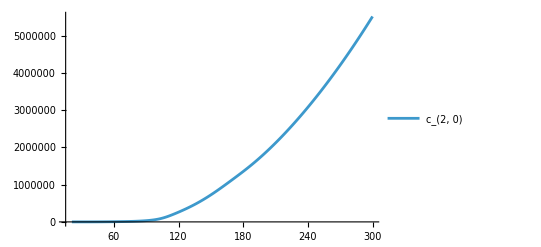

```mathematica
chi0=Flatten[Import["./chi0.dat"]];
chi1=Flatten[Import["./chi1.dat"]];
chi2=Flatten[Import["./chi2.dat"]];
chi3=Flatten[Import["./chi3.dat"]];
chi4=Flatten[Import["./chi4.dat"]];
chi5=Flatten[Import["./chi5.dat"]];
chi6=Flatten[Import["./chi6.dat"]];
chi7=Flatten[Import["./chi7.dat"]];
chi8=Flatten[Import["./chi8.dat"]];
T=Flatten[Table[21+(i-1),{i,1,280}]];
(*c0=Transpose[{T/184,chi0/T^4}];
c1=Transpose[{T,-4*chi0/T^5+chi1/T^4}];
c2=Transpose[{T,20*chi0/T^6-8*chi1/T^5+chi2/T^4}];
c3=Transpose[{T,-(120 chi0)/T^7+(60 chi1)/T^6-(12 chi2)/T^5+chi3/T^4}];
c4=Transpose[{T,(840 chi0)/T^8-(480 chi1)/T^7+(120 chi2)/T^6-(16 chi3)/T^5+chi4/T^4}];
cs2=Transpose[{T/184,chi1/(T*chi2)}];*)
ListLinePlot[Transpose[{T,chi2}],PlotRange->All,PlotLegends->{"c_(2, 0)"}]
```

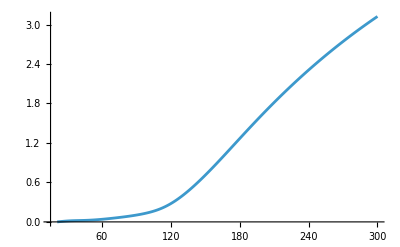

```mathematica
ListLinePlot[Transpose[{T,(chi0-chi0[[1]])/T^4}],PlotRange->All]
```

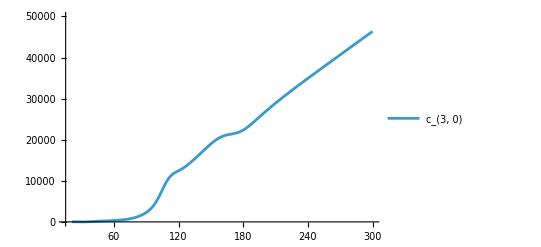

```mathematica
ListLinePlot[Transpose[{T,chi3}],PlotRange->{All,{-0000,50000}},PlotLegends->{"c_(3, 0)"}]
```

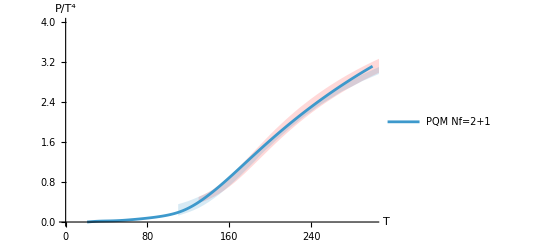

```mathematica
PlotP=Show[ListLinePlot[{Transpose[{T/1,(chi0-chi0[[1]])/T^4}],Hotpdown,Hotpup},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.,300},{0,4}}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T","P/T^4"}]
```

## Temperature Fluctuations

```mathematica
c1=chi1;
c2=T^2(1/chi2)^1;
c3=-T^5(1/chi2)^3(chi3);
c4=T^8(3(1/chi2)^5(chi3)^2-(1/chi2)^4 chi4);
```

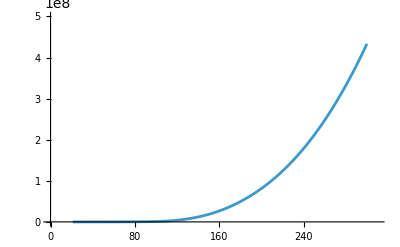

```mathematica
ListLinePlot[Transpose[{T,chi1}],PlotRange->{{0,310},{0.01,5*10^8}},ScalingFunctions->Automatic]
```

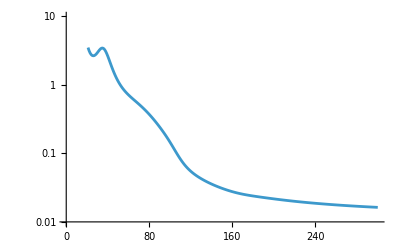

```mathematica
ListLinePlot[Transpose[{T,c2}],PlotRange->{{0,300},{0.01,10}},ScalingFunctions->"Log"]
```

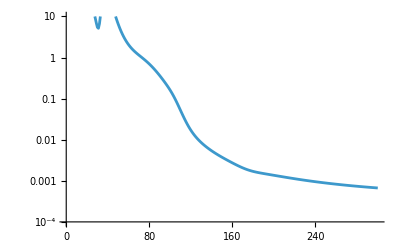

```mathematica
ListLinePlot[Transpose[{T,-c3}],PlotRange->{{0,300},{10,0.0001}},ScalingFunctions->"Log"]
```

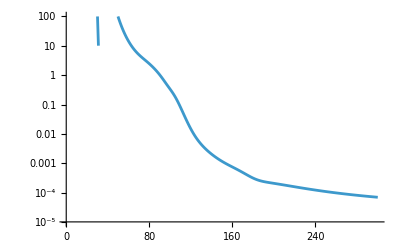

```mathematica
ListLinePlot[Transpose[{T,c4}],PlotRange->{{0,300},{0.00001,100}},ScalingFunctions->"Log"]
```